```mathematica
SetDirectory["C:\\Users\\joebr\\OneDrive\\Documents\\QPO Research\\Mathematica Code\\Spherical Eigenvalues"]
FileNames[]
```

SetDirectory::cdir: Cannot set current directory to C:\Users\joebr\OneDrive\Documents\QPO Research\Mathematica Code\Spherical Eigenvalues.

$Failed

{c100ExtraModes20.m,c100ExtraModes30.m,c100ExtraModes40.m,c100ExtraModes50.m,c100ExtraModes.m,c100ExtraModes.nb,c100mu0evsl30n150.mx,c100mu0evsl30n50.mx,c100mu0evsl50n50.Mat,c100mu0evsl50n50.mx,c100mu0evsl50n50np48.mx,c100testevsl4n47.mx,c100XMl10.Mx,c100XMl20.Mx,c100XMl30.Mx,c100XMl50.Mx,c10mu0evsl50n50.Mat,c10mu0evsl50n50.mx,c10mu0evsl50n50np48.mx,c3mu0evsl50n50.Mat,c3mu0evsl50n50.mx,c3mu0evsl50n50np48.mx,c5evsl20n20.Mx,CoupledRootFinder.nb,CRFc100l30n150.m,CRFc100l30n50.m,CRFc100l30n50nb.nb,CRFc100l30n50p.m,CRFc100l50n50.m,CRFc10l50n50.m,CRFc3l50n50.m,EFJob.sh,evaluesc10,evaluesc100,evaluesc100l20n50,evaluesc2,evaluesc5,RootFinder.nb,SphericalEigenvalues.nb,VariableMu}

```mathematica
<<evaluesc580
```

## Old

```mathematica
(* Import Eigenvalues *)
```

```mathematica
se2=Import["evalues1a"];
se10=Import["evalues1b"];
```

```mathematica
(* Convert strings to tables *)
```

```mathematica
Do[MakeExpression[StringDrop[StringJoin[se2[[j,1]],",",se2[[j,2]]],-1],StandardForm]//ReleaseHold,{j,8,Length[se2]}]//Quiet
se2at=Array[ww,{10,10}];
```

```mathematica
se5a=Array[xx,{10,25}];
```

```mathematica
se5a[[1,All]]
```

```mathematica
xx[1,2]
```

4.142824549436289396336757957909024292326427941476826996269817876+0.29272256127533699125201359439635958503508715315453683390660398 ⅈ

```mathematica
Do[MakeExpression[StringDrop[StringJoin[se10[[j,1]],",",se10[[j,2]]],-1],StandardForm]//ReleaseHold,{j,8,Length[se10]}]//Quiet
se10a=Array[ww,{10,10}];
```

```mathematica
(* Plots *)
```

```mathematica
se2acpl=Table[{Re[se2a[[n,l]]],Im[se2a[[n,l]]]},{l,1,10},{n,1,10}];
```

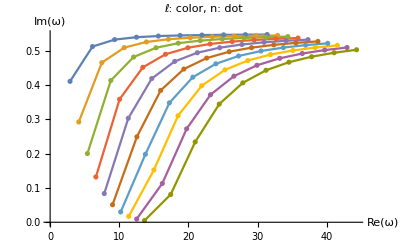

```mathematica
Show[ListPlot[se2acpl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[se2acpl],PlotLabel->"ℓ: color, n: dot"]
```

```mathematica
se10acpl=Table[{Re[se10a[[n,l]]],Im[se10a[[n,l]]]},{l,1,10},{n,1,10}];
```

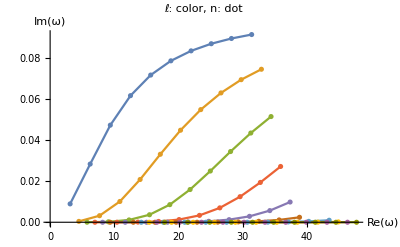

```mathematica
Show[ListPlot[se10acpl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[se10acpl],PlotLabel->"ℓ: color, n: dot"]
```

### c_2=2

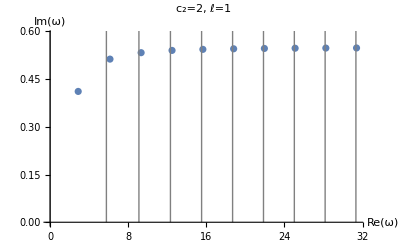

```mathematica
ListPlot[{Re[se2a[[#,1]]],Im[se2a[[#,1]]]}&/@Range[1,10],PlotRange->{0,.59},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=2, ℓ=1"];
ListPlot[{{zf[[1,#]],0},{zf[[1,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%]
```

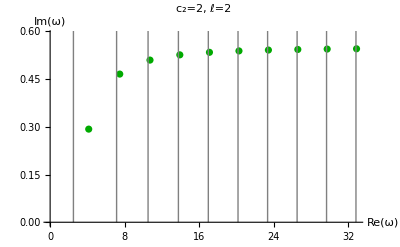

```mathematica
ListPlot[{Re[se2a[[#,2]]],Im[se2a[[#,2]]]}&/@Range[1,10],PlotStyle->Darker[Green],PlotRange->{0,.59},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=2, ℓ=2"];
ListPlot[{{zf[[2,#]],0},{zf[[2,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%]
```

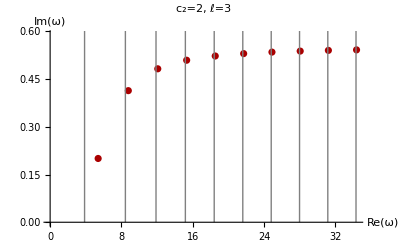

```mathematica
ListPlot[{Re[se2a[[#,3]]],Im[se2a[[#,3]]]}&/@Range[1,10],PlotStyle->Darker[Red],PlotRange->{0,.59},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=2, ℓ=3"];
ListPlot[{{zf[[3,#]],0},{zf[[3,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%]
```

### c_2=10

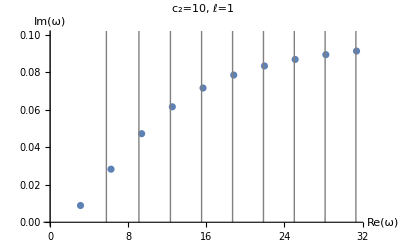

```mathematica
ListPlot[{Re[se10a[[#,1]]],Im[se10a[[#,1]]]}&/@Range[1,10],PlotRange->{0,.1},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=10, ℓ=1"];
ListPlot[{{zf[[1,#]],0},{zf[[1,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%]
```

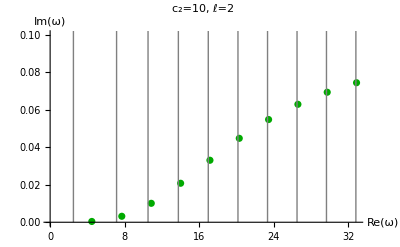

```mathematica
ListPlot[{Re[se10a[[#,2]]],Im[se10a[[#,2]]]}&/@Range[1,10],PlotStyle->Darker[Green],PlotRange->{0,.1},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=10, ℓ=2"];
ListPlot[{{zf[[2,#]],0},{zf[[2,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%]
```

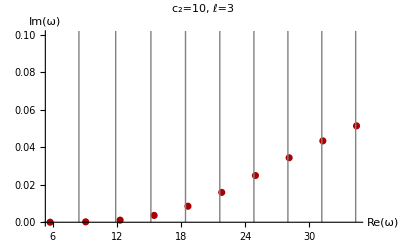

```mathematica
ListPlot[{Re[se10a[[#,3]]],Im[se10a[[#,3]]]}&/@Range[1,10],PlotStyle->Darker[Red],PlotRange->{0,.1},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=10, ℓ=3"];
ListPlot[{{zf[[3,#]],0},{zf[[3,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%]
```

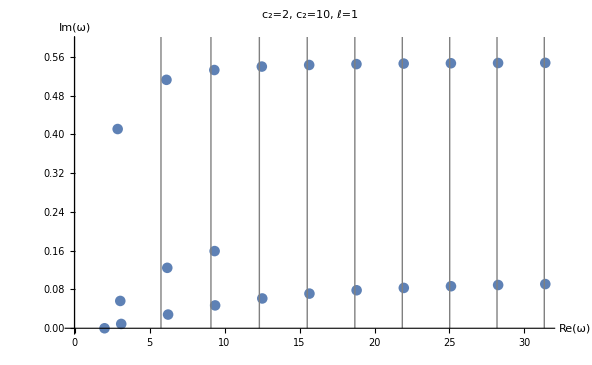

```mathematica
ListPlot[{Re[se2at[[#,1]]],Im[se2at[[#,1]]]}&/@Range[1,10],PlotRange->{0,.59},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=2, c_2=10, ℓ=1"];
ListPlot[{Re[se5a[[#,1]]],Im[se5a[[#,1]]]}&/@Range[1,10],PlotRange->{0,.1},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=2, c_2=10, ℓ=1"];
ListPlot[{Re[se10a[[#,1]]],Im[se10a[[#,1]]]}&/@Range[1,10],PlotRange->{0,.1},AxesLabel->{"Re(ω)","Im(ω)"},PlotLabel->"c_2=2, c_2=10, ℓ=1"];
ListPlot[{{zf[[1,#]],0},{zf[[1,#]],1}}&/@Range[1,10],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%%%,%%%,%%,%]
```

```mathematica
{.53,.16,.04}.DiagonalMatrix[{2,5,10}]
```

{1.06,0.8,0.4}

## New

```mathematica
(* Import *)
```

```mathematica
c5mu1evs=Import["c5mu1evs.Mat"][[1]];
```

```mathematica
c5mu2evs=Import["c5mu2evs.Mat"][[1]];
```

```mathematica
c5mu0p5evs=Import["c5mu0p5evs.Mat"][[1]];
```

```mathematica
c5mu6evs=Import["c5mu6evs.Mat"][[1]];
```

```mathematica
c1mu0p5evs=Import["c1mu0p5evs.Mat"][[1]];
```

```mathematica
c1mu0p25evs=Import["c1mu0p25evs.Mat"][[1]];
```

```mathematica
c1mu0p125evs=Import["c1mu0p125evs.Mat"][[1]];
```

```mathematica
c1mu0p05evs=Import["c1mu0p05evs.Mat"][[1]];
```

```mathematica
(* Plot *)
```

### Same C

```mathematica
c1mu0p5pl=Table[{Re[c1mu0p5evs[[n,l]]],Im[c1mu0p5evs[[n,l]]]},{l,1,1},{n,3,7}];
```

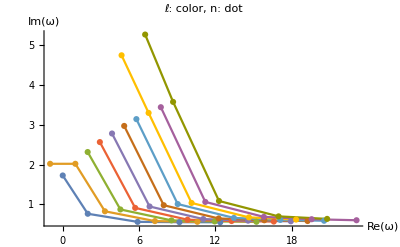

```mathematica
Show[ListPlot[c1mu0p5pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c1mu0p5pl],PlotLabel->"ℓ: color, n: dot",PlotRange->All]
```

```mathematica
c1mu0p25pl=Table[{Re[c1mu0p25evs[[n,l]]],Im[c1mu0p25evs[[n,l]]]},{l,1,1},{n,3,7}];
```

```mathematica
c1mu0p125pl=Table[{Re[c1mu0p125evs[[n,l]]],Im[c1mu0p125evs[[n,l]]]},{l,1,1},{n,3,7}];
```

```mathematica
c1mu0p05pl=Table[{Re[c1mu0p05evs[[n,l]]],Im[c1mu0p05evs[[n,l]]]},{l,1,1},{n,3,7}];
```

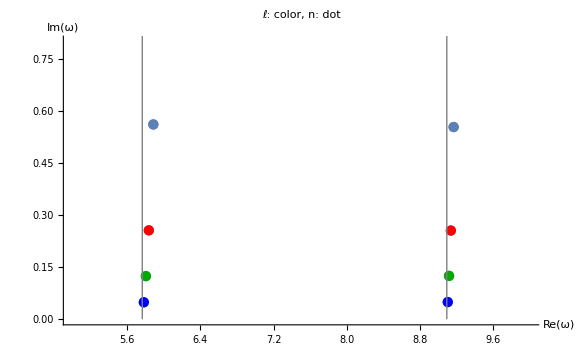

```mathematica
Show[ListPlot[c1mu0p125pl(*,Joined->True*),AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c1mu0p125pl,PlotStyle->Darker[Green]],PlotLabel->"ℓ: color, n: dot"(*,PlotRange->All*)];
Show[ListPlot[c1mu0p05pl(*,Joined->True*),AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c1mu0p05pl,PlotStyle->Blue],PlotLabel->"ℓ: color, n: dot"(*,PlotRange->All*)];
Show[ListPlot[c1mu0p25pl(*,Joined->True*),AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c1mu0p25pl,PlotStyle->Red],PlotLabel->"ℓ: color, n: dot"(*,PlotRange->All*)];
Show[ListPlot[c1mu0p5pl,(*Joined->True,*)AxesLabel->{"Re(ω)","Im(ω)"},ImageSize->Large],ListPlot[c1mu0p5pl],PlotLabel->"ℓ: color, n: dot"(*,PlotRange->All*)];
ListPlot[{{zf[[1,#]],0},{zf[[1,#]],5}}&/@Range[1,7],Joined->True,PlotStyle->Directive[Thin,Gray]];
Show[%%,%%%,%%%%,%%%%%,%,PlotRange->{{5,10},{0,.8}},AxesOrigin->Automatic]
```

```mathematica
{.554,.253,.126,.048} .DiagonalMatrix[{2,4,8,20}]
```

{1.108,1.012,1.008,0.96}

### Different C

```mathematica
c5mu1pl=Table[{Re[c5mu1evs[[n,l]]],Im[c5mu1evs[[n,l]]]},{l,1,10},{n,1,10}];
```

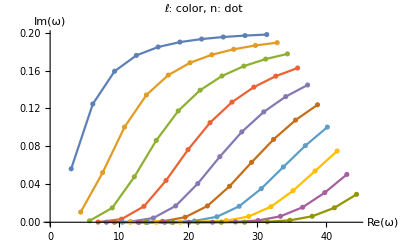

```mathematica
Show[ListPlot[c5mu1pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu1pl],PlotLabel->"ℓ: color, n: dot"]
```

```mathematica
c5mu6pl=Table[{Re[c5mu6evs[[n,l]]],Im[c5mu6evs[[n,l]]]},{l,1,10},{n,1,10}];
```

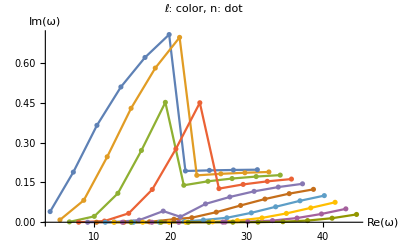

```mathematica
Show[ListPlot[c5mu6pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"},PlotRange->All],ListPlot[c5mu6pl],PlotLabel->"ℓ: color, n: dot"]
```

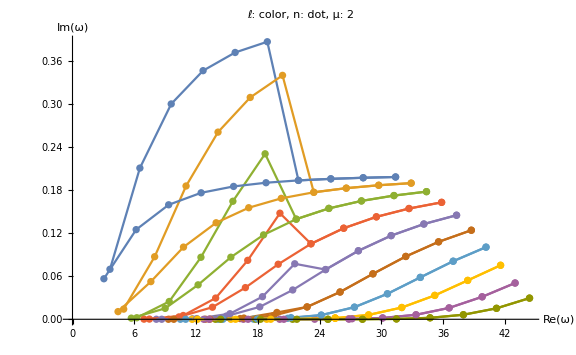

```mathematica
Show[ListPlot[c5mu2pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu1pl],ListPlot[c5mu1pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu2pl],PlotLabel->"ℓ: color, n: dot, μ: 2",ImageSize->Large]
```

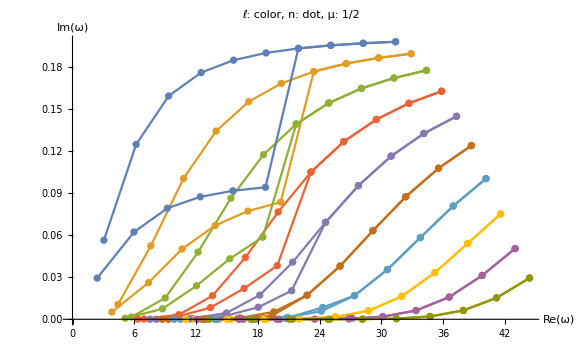

```mathematica
Show[ListPlot[c5mu1pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu1pl],ListPlot[c5mu0p5pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu0p5pl],PlotLabel->"ℓ: color, n: dot, μ: 1/2",ImageSize->Large]
```

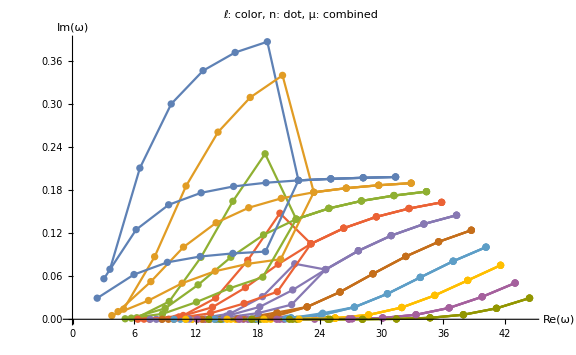

```mathematica
Show[ListPlot[c5mu2pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu1pl],ListPlot[c5mu1pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu2pl],ListPlot[c5mu0p5pl,Joined->True,AxesLabel->{"Re(ω)","Im(ω)"}],ListPlot[c5mu0p5pl],PlotLabel->"ℓ: color, n: dot, μ: combined",ImageSize->Large]
```

## Eigenfunctions

```mathematica
j[l_,r_]:=SphericalBesselJ[l,r];
h1[l_,r_]:=SphericalHankelH1[l,r];
h2[l_,r_]:=SphericalHankelH2[l,r];
```

```mathematica
A2l[l_,ω_]=((ⅈ Rs ω)/c2)((1-α)j[l,(Rs ω)/c1](((Rs ω)/c2)h2[l-1,(Rs ω)/c2]-(l+2)h2[l,(Rs ω)/c2])-(1+α)h2[l,(Rs ω)/c2](((Rs ω)/c2)j[l-1,(Rs ω)/c1]-c1/c2(l+2)j[l,(Rs ω)/c1]));
A1l[l_,ω_]=-((ⅈ Rs ω)/c2)((1-α)j[l,(Rs ω)/c1](((Rs ω)/c2)h1[l-1,(Rs ω)/c2]-(l+2)h1[l,(Rs ω)/c2])-(1+α)h1[l,(Rs ω)/c2](((Rs ω)/c2)j[l-1,(Rs ω)/c1]-c1/c2(l+2)j[l,(Rs ω)/c1]));
```

```mathematica
Table[Piecewise[{{Re[(1-α)(*∂_r *)(D[j[l,ω/c1 r],r]-j[l,ω/c1 r]/r)],0≤r≤1},{Re[1/2(*∂_r *)(A2l[l,ω](D[h1[l,ω/c2 r],r]-h1[l,ω/c2 r]/r)(*+A1l[l,ω]h2[l,ω/c2 r]*))],1<r}}]/.ω->Conjugate[ww[n,l]]/.{n->2(*,n->5*)},{l,1,10}];
Plot[%//Evaluate,{r,0,2},PlotRange->All,ImageSize->800,Frame->True,FrameLabel->{"r","r ∂_r (u_ϕ/r)"},PlotLabel->(*"ℓ=2, *)"n=2",GridLines->{{1},{0}},AspectRatio->1/3]
```

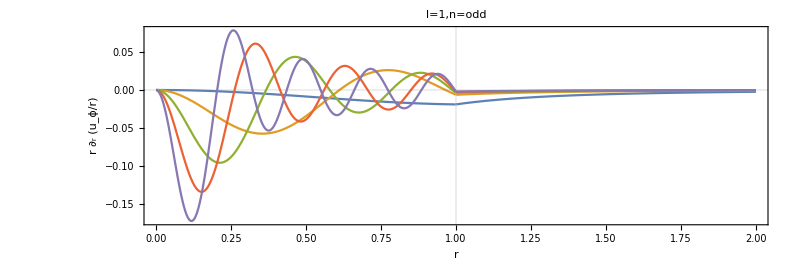

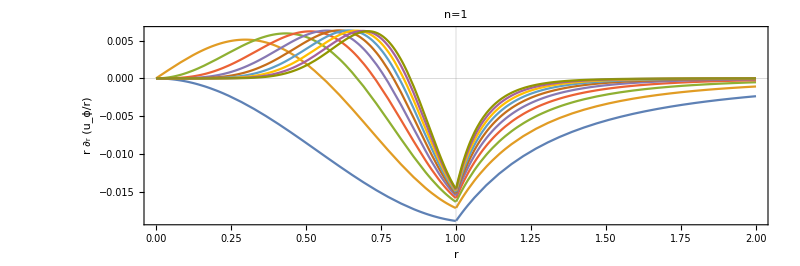

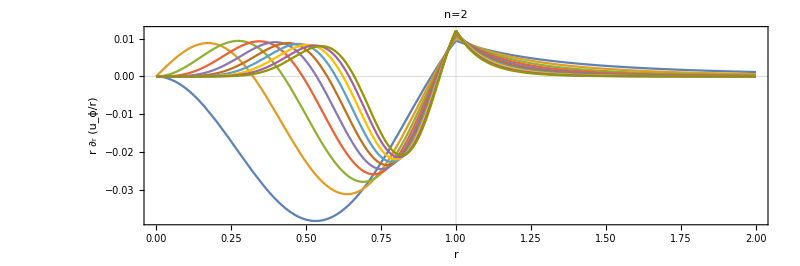

```mathematica
Table[-.001Log10[Im[ww[n,l]]],{l,10},{n,20}];
```

```mathematica
Table[Abs[Re[(1-α)(*∂_r *)(D[j[l,ω/c1 r],r]-j[l,ω/c1 r]/r)(*-(1/2∂_r (A2l[l,ω](D[h1[l,ω/c2 r],r]-h1[l,ω/c2 r]/r)))*)]]/.{r->1,ω->Conjugate[ww[n,l]]},{l,10},{n,20}];
```

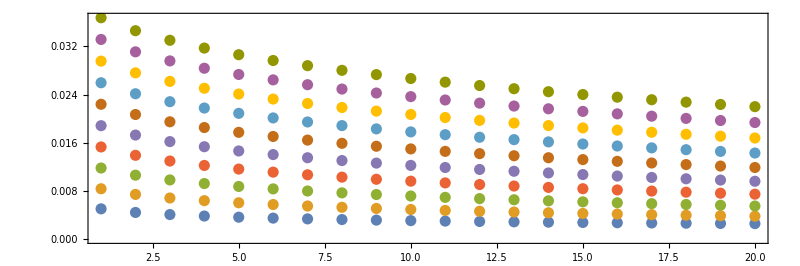

```mathematica
ListPlot[%687(*%678*),PlotRange->All,Frame->True,AspectRatio->1/3,ImageSize->800,PlotStyle->PointSize[.01]]
```

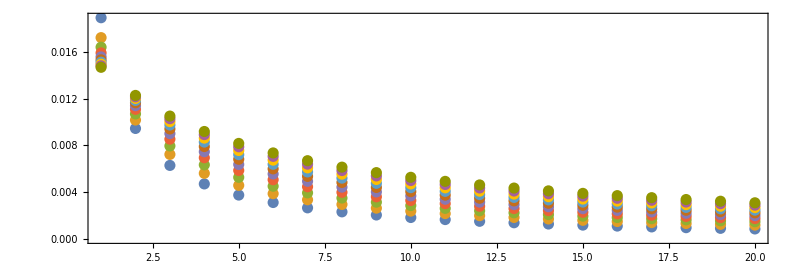

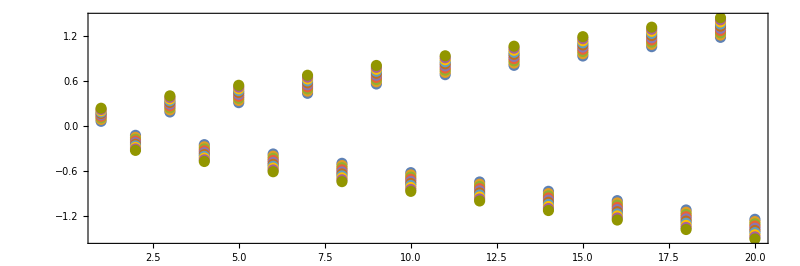

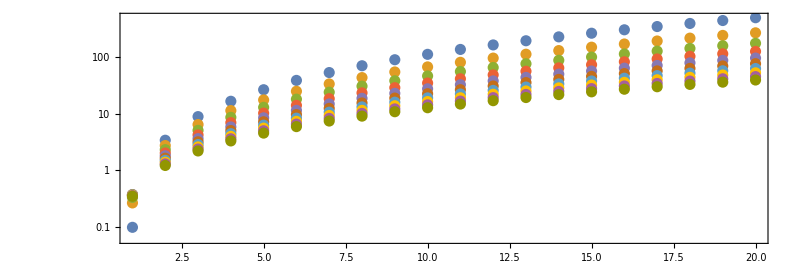

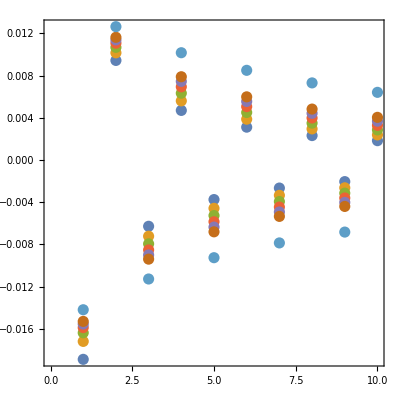

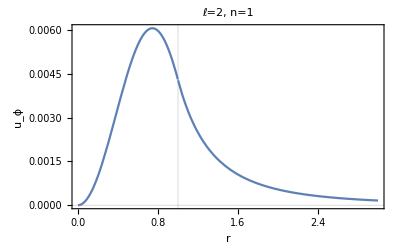

```mathematica
Piecewise[{{(1-α)j[l,ω/c1 r],0≤r≤1},{1/2(A2l[l,ω]h1[l,ω/c2 r](*+A1l[l,ω]h2[l,ω/c2 r]*)),1<r}}]/.ω->Conjugate[ww[n,l]]/.{l->2,n->1};
Plot[Re[%]//Evaluate,{r,0,3},PlotRange->All,ImageSize->400,Frame->True,FrameLabel->{"r","u_ϕ"},PlotLabel->"ℓ=2, n=1",GridLines->{{1},{0}}]
```

```mathematica
ww[1,2]
```

4.49325957193181575185024298565177044542938218483024218575886253+4.526417251174978958486629783217866471402286828865752639837245239×10^-9 ⅈ

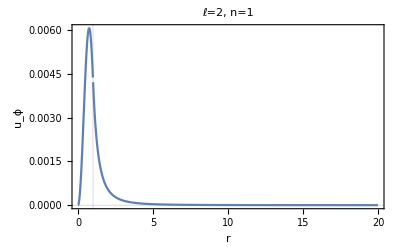

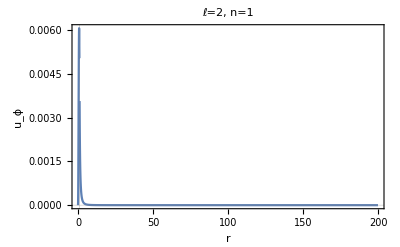

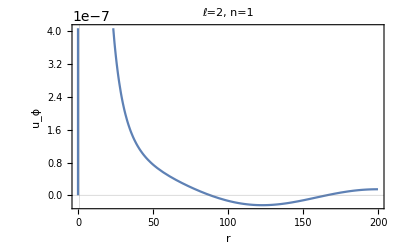

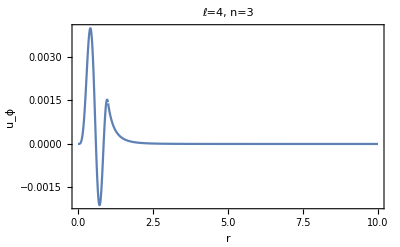

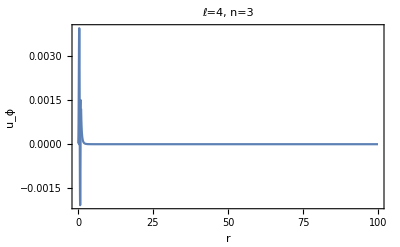

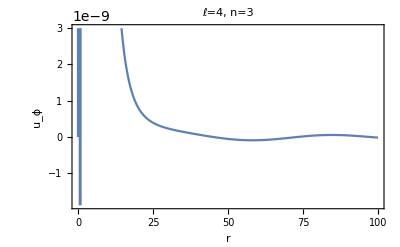

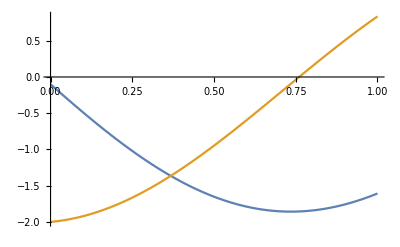

```mathematica
Plot[ReIm[-ⅈ(2-.1ⅈ)Exp[-ⅈ(2-.1ⅈ) t]]//Evaluate,{t,0,1}]
```

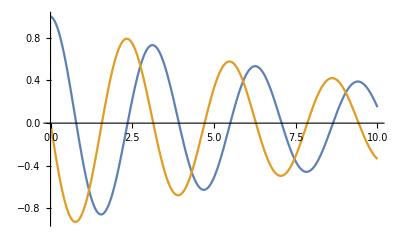

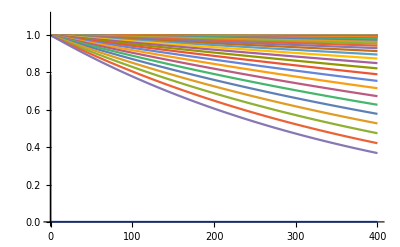

```mathematica
Table[Exp[- 100t Im[ww[n,l]]],{n,50},{l,{4}}]//Flatten;
Plot[%,{t,0,400},PlotRange->{0,1.1}]
```

```mathematica
Table[Short[ColorData[i,"ColorList"],4],{i,60,70}]//MatrixForm
```

({RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616]}
{RGBColor[0.70135, 0.093019, 0.00140383],RGBColor[0.289647, 0.222614, 0.484169],RGBColor[0.98677, 0.98793, 0.458686],RGBColor[0.42948, 0.524086, 0.719463],RGBColor[0.30808, 0.443137, 0.124895],RGBColor[0.895125, 0.71606, 0.0964523],RGBColor[0.138415, 0.184848, 0.429862],RGBColor[0.882353, 0.0253147, 0.11165],RGBColor[0.895125, 0.870893, 0.632624]}
{RGBColor[0.90045, 0.765209, 0.745602],RGBColor[0.864256, 0.544503, 0.601099],RGBColor[0.719463, 0.374975, 0.35935],RGBColor[0.312215, 0.134813, 0.182895],RGBColor[0.488685, 0.199069, 0.220294],RGBColor[0.963806, 0.945785, 0.623575],RGBColor[0.299687, 0.352941, 0.114382],RGBColor[0.606516, 0.669688, 0.306233],RGBColor[1, 0.886915, 0.754116],RGBColor[0.704433, 0.864256, 0.469459],RGBColor[1, 0.978103, 0.943175],RGBColor[0.280537, 0.234745, 0.149096],RGBColor[0.338262, 0.480644, 0.141192]}
{RGBColor[0.73, 0.24506099999999992, 0.1971],RGBColor[0.1971, 0.5022473119339774, 0.73],RGBColor[0.5356156238679548, 0.73, 0.1971],RGBColor[0.5712760641980676, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.5379077522640902],RGBColor[0.73, 0.5045394403301129, 0.1971],RGBColor[0.1971, 0.24276887160386468, 0.73],RGBColor[0.27613718353784195, 0.73, 0.1971],RGBColor[0.73, 0.1971, 0.6292454954718195],RGBColor[0.1971, 0.662613807405797, 0.73],RGBColor[0.6959821193397744, 0.73, 0.1971],RGBColor[0.4109095687262533, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.3775412567922707],RGBColor[0.73, 0.34417294485828825, 0.1971],RGBColor[0.1971, 0.4031353670756841, 0.73]}
{Hue[0.5, 0.5, 0.4],Hue[0.11, 0.75, 0.8],Hue[0.04, 1, 0.8],Hue[0.5, 0.5, 0.6],Hue[0.67, 0.33, 0.5],Hue[0.33, 0.5, 0.6],Hue[0, 0.67, 0.6],Hue[0.17, 0.9, 0.7],Hue[0, 0.5, 0.6],Hue[0.17, 0.33, 0.6]}
{Hue[0.64, 0.5, 0.7],Hue[0.11, 0.75, 0.7],Hue[0.5, 0.7, 0.6],Hue[0.2, 0.66, 0.66],Hue[0.7, 0.4, 0.8],Hue[0.15, 0.67, 0.75],Hue[0.5, 0.6, 0.7],Hue[0.17, 0.6, 0.6],Hue[0.35, 0.33, 0.75],Hue[0.25, 0.67, 0.6]}
{Hue[0.61, 0.7, 1],Hue[0.17, 0.4, 0.65],Hue[0.64, 0.5, 0.75],Hue[0.45, 0.4, 0.7],Hue[0.55, 0.8, 0.6],Hue[0.64, 0.2, 0.7],Hue[0.4, 0.5, 0.5],Hue[0.56, 0.6, 0.85],Hue[0.58, 0.5, 0.6],Hue[0.45, 0.7, 0.7]}
{Hue[0, 1, 1],Hue[0.1, 0.7, 0.9],Hue[0, 0.75, 0.8],Hue[0.05, 0.8, 1],Hue[0.05, 1, 0.8],Hue[0, 0.7, 1],Hue[0, 1, 0.7],Hue[0, 0.8, 0.9],Hue[0.05, 0.9, 0.6],Hue[0.05, 0.7, 0.8]}
{Hue[0.55, 1, 0.7],Hue[0.06, 1, 0.9],Hue[0.25, 1, 0.55],Hue[0.11, 0.9, 0.85],Hue[0.5, 1, 0.5],Hue[0.2, 1, 0.7],Hue[0.08, 1, 0.7],Hue[0.5, 0.8, 0.75],Hue[0.45, 1, 0.5],Hue[0.6, 0.5, 0.9]}
{Hue[0.12, 0.8, 0.8],Hue[0.17, 0.6, 0.5],Hue[0.1, 0.83, 0.96],Hue[0.1, 1, 0.7],Hue[0.11, 0.6, 0.8],Hue[0.06, 0.75, 0.8],Hue[0.13, 0.67, 0.96],Hue[0.11, 0.75, 0.64],Hue[0.11, 0.5, 0.96],Hue[0.08, 0.67, 0.85]}
{Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9]})

```mathematica
zshift=.766;
τ=.012;
```

```mathematica
zshift(2π (*2.35*)τ)^-1 (.01)/(.000025)
```

1633.99

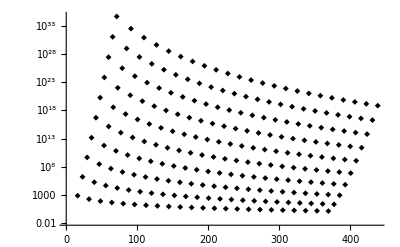

```mathematica
ListLogPlot[Table[{zshift(2π 2.4τ)^-1 Chop[SP`zff[[l,n]]],(τ)/((.01)^(2l+1)Chop[SP`zff[[l,n]]]^(2l)/((2l-1)!!)^2)zshift},{l,10},{n,23}],PlotStyle->Black,PlotMarkers->{"◆", 6}]
```

### c100

```mathematica
LvFtab=Table[{ zshift(2π (*2.4*)τ)^-1 Re[ww[n,l]],(zshift/τ)Im[ww[n,l]]},{l,10},{n,50}];
LvGtab=Table[{zshift(2π (*2.4*)τ)^-1 Chop[SP`zff[[l,n]]],(zshift/τ)((.01)^(2l+1)Chop[SP`zff[[l,n]]]^(2l)/((2l-1)!!)^2)},{l,10},{n,23}];
```

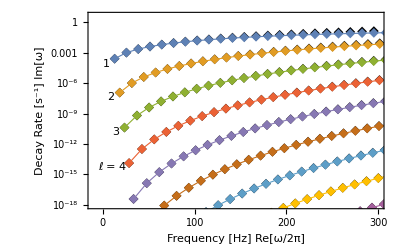

```mathematica
Show[ListLogPlot[LvGtab,(*Joined->True,*)PlotStyle->Directive[Black,Thickness[.002]],PlotMarkers->Style["◆",10],PlotRange->{{-10,300},{1*^-18,10^0.6}},Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω/2π]","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},
GridLines->{{},{300^-1}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{1,"1",{.03,0}},{10^-3,"",{.03,0}},{300^-1,"300^-1",0},{10^-6,"10^-6",{.03,0}},{10^-9,"",{.03,0}},{10^-12,"10^-12",{.03,0}},{10^-15,"",{.03,0}},{10^-18,"10^-18",{.03,0}},{10^-1,""},{10^-2,""},{10^-4,""},{10^-5,""},{10^-7,""},{10^-8,""},{10^-10,""},{10^-11,""},{10^-13,""},{10^-14,""},{10^-16,""},{10^-17,""}},(*Right*)Automatic},{(*Bottom*){{0,"0",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"50",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"100",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"150",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"200",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"250",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"300",{.03,0}}},(*Top*){{0,"",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"",{.03,0}}}}}],
ListLogPlot[LvFtab,Joined->True,PlotMarkers->{"◆", 10},PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 4",{-5,-34},{-1,-1}],
Text["3",{10,-26},{-1,-1}],
Text["2",{5,-18},{-1,-1}],
Text["1",{0,-10.5},{-1,-1}]}]]
```

```mathematica
Table[{10 l,""},{l,0,30}]
```

{{0,},{10,},{20,},{30,},{40,},{50,},{60,},{70,},{80,},{90,},{100,},{110,},{120,},{130,},{140,},{150,},{160,},{170,},{180,},{190,},{200,},{210,},{220,},{230,},{240,},{250,},{260,},{270,},{280,},{290,},{300,}}

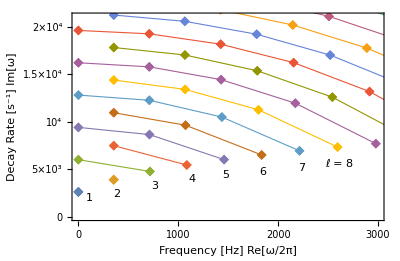

```mathematica
LvHtab=Table[{ zshift(2π (*2.4*)τ)^-1 xmrtot[[l,n,1]],(zshift/τ)xmrtot[[l,n,2]]},{l,20},{n,Length[xmrtot[[l]]]}];
LvItab=Table[{zshift(2π (*2.4*)τ)^-1 Chop[xmapprox[[l,n,1]]],(zshift/τ)(xmapprox[[l,n,2]])},{l,20},{n,Length[xmapprox[[l]]]}];

Show[ListPlot[LvHtab,Joined->False,PlotStyle->Thickness[.002],(*PlotStyle->Black,*)PlotMarkers->Style["◆",10],PlotRange->{{-4,3000},{0,21000}},AspectRatio->1/(.945GoldenRatio),Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω/2π]","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},GridLines->{{},{}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{0,"0"},{5 10^3,"5×10^3",{.03,0}},{10^4,"10^4",{.03,0}},{1.5 10^4,"1.5×10^4",{.03,0}},{2 10^4,"2×10^4",{.03,0}},
{1000,""},{2000,""},{3000,""},{4000,""},{6000,""},{7000,""},{8000,""},{9000,""},
{11000,""},{12000,""},{13000,""},{14000,""},{16000,""},{17000,""},{18000,""},{19000,""}},
(*Right*){{1000,""},{2000,""},{3000,""},{4000,""},{5000,"",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"",{.03,0}},{16000,""},{17000,""},{18000,""},{19000,""},{20000,"",{.03,0}}}},{(*Bottom*){{0,"0",{0,0}},{100,""},{200,""},{300,""},{400,""},{500,"500",{.03,0}},{600,""},{700,""},{800,""},{900,""},{1000,"1000",{.03,0}},{1100,""},{1200,""},{1300,""},{1400,""},{1500,"1500",{.03,0}},{1600,""},{1700,""},{1800,""},{1900,""},{2000,"2000",{.03,0}},{2100,""},{2200,""},{2300,""},{2400,""},{2500,"2500",{.03,0}},{2600,""},{2700,""},{2800,""},{2900,""},{3000,"3000"}},
(*Top*){{0,"",{0,0}},{100,""},{200,""},{300,""},{400,""},{500,"",{.03,0}},{600,""},{700,""},{800,""},{900,""},{1000,"",{.03,0}},{1100,""},{1200,""},{1300,""},{1400,""},{1500,"",{.03,0}},{1600,""},{1700,""},{1800,""},{1900,""},{2000,"",{.03,0}},{2100,""},{2200,""},{2300,""},{2400,""},{2500,"",{.03,0}},{2600,""},{2700,""},{2800,""},{2900,""},{3000,""}}}}],
ListPlot[LvHtab,PlotMarkers->{"◆", 10},Joined->True,PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 8",{2470,5000},{-1,-1}],
Text["7",{2200,4600},{-1,-1}],
Text["6",{1810,4200},{-1,-1}],
Text["5",{1440,3800},{-1,-1}],
Text["4",{1100,3400},{-1,-1}],
Text["3",{730,2700},{-1,-1}],
Text["2",{350,1800},{-1,-1}],
Text["1",{70,1400},{-1,-1}]}]]
```

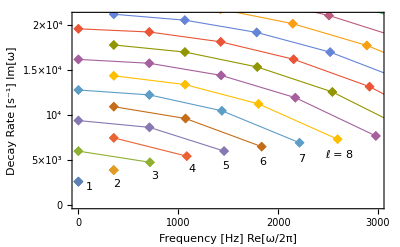

```mathematica
|
```

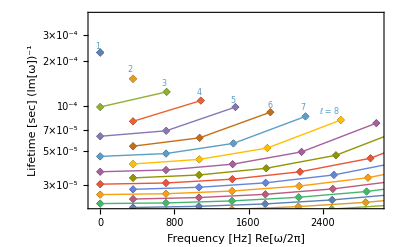

### c1000

```mathematica
τ
zshift
ww[0,1]
```

0.03

0.77

1001. ⅈ

```mathematica
LvFtab=Table[{ zshift(2π τ)^-1 Re[ww[n,l]],(zshift/τ)Im[ww[n,l]]},{l,10},{n,50}];
LvGtab=Table[{zshift(2π τ)^-1 Chop[SP`zff[[l,n]]],(zshift/τ)((.001)^(2l+1)Chop[SP`zff[[l,n]]]^(2l)/((2l-1)!!)^2)},{l,10},{n,23}];
```

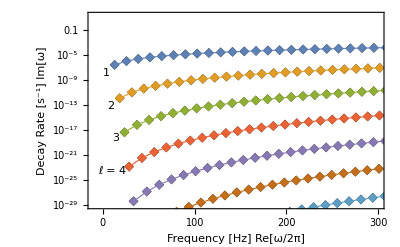

```mathematica
Show[ListLogPlot[LvGtab,(*Joined->True,*)PlotStyle->Directive[Black,Thickness[.002]],PlotMarkers->Style["◆",10],PlotRange->{{-10,300},{1*^-29,10^1.2}},Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω/2π]","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},
GridLines->{{},{300^-1}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{1,"1",{.03,0}},{10^-3,"",{.03,0}},{300^-1,"300^-1",0},{10^-6,"10^-6",{.03,0}},{10^-9,"",{.03,0}},{10^-12,"10^-12",{.03,0}},{10^-15,"",{.03,0}},{10^-18,"10^-18",{.03,0}},{10^-21,"",{.03,0}},{10^-24,"10^-24",{.03,0}},{10^-27,"",{.03,0}},{10^-1,""},{10^-2,""},{10^-4,""},{10^-5,""},{10^-7,""},{10^-8,""},{10^-10,""},{10^-11,""},{10^-13,""},{10^-14,""},{10^-16,""},{10^-17,""},{10^-19,""},{10^-20,""},{10^-22,""},{10^-23,""},{10^-25,""},{10^-26,""},{10^-28,""}},(*Right*)Automatic},{(*Bottom*){{0,"0",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"50",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"100",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"150",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"200",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"250",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"300",{.03,0}}},(*Top*){{0,"",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"",{.03,0}}}}}],
ListLogPlot[LvFtab,Joined->True,PlotMarkers->{"◆", 10},PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 4",{-5,-56},{-1,-1}],
Text["3",{10,-44},{-1,-1}],
Text["2",{5,-32},{-1,-1}],
Text["1",{0,-20},{-1,-1}]}]]
```

```mathematica
Table[{10 l,""},{l,0,30}]
```

```mathematica
LvHtab=Table[{ zshift(2π τ)^-1 ReIm[xmth][[l,n,1]],(zshift/τ)ReIm[xmth][[l,n,2]]},{l,20},{n,Length[xmrtot[[l]]]}];
```

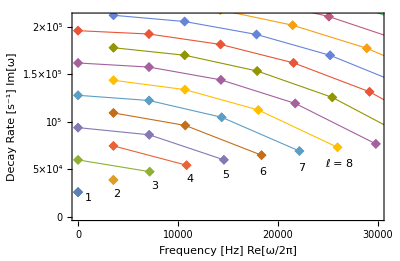

```mathematica
Show[ListPlot[LvHtab,Joined->False,PlotStyle->Thickness[.002],(*PlotStyle->Black,*)PlotMarkers->Style["◆",10],PlotRange->{{-4,30000},{0,210000}},AspectRatio->1/(.945GoldenRatio),Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω/2π]","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},GridLines->{{},{}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{0,"0"},{5 10^4,"5×10^4",{.03,0}},{10^5,"10^5",{.03,0}},{1.5 10^5,"1.5×10^5",{.03,0}},{2 10^5,"2×10^5",{.03,0}},
{10000,""},{20000,""},{30000,""},{40000,""},{60000,""},{70000,""},{80000,""},{90000,""},
{110000,""},{120000,""},{130000,""},{140000,""},{160000,""},{170000,""},{180000,""},{190000,""}},
(*Right*){{10000,""},{20000,""},{30000,""},{40000,""},{50000,"",{.03,0}},{60000,""},{70000,""},{80000,""},{90000,""},{100000,"",{.03,0}},{110000,""},{120000,""},{130000,""},{140000,""},{150000,"",{.03,0}},{160000,""},{170000,""},{1800000,""},{190000,""},{200000,"",{.03,0}}}},{(*Bottom*){{0,"0",{0,0}},{1000,""},{2000,""},{3000,""},{4000,""},{5000,"5000",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"10000",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"15000",{.03,0}},{16000,""},{170000,""},{18000,""},{19000,""},{20000,"20000",{.03,0}},{21000,""},{22000,""},{23000,""},{24000,""},{25000,"25000",{.03,0}},{26000,""},{27000,""},{28000,""},{29000,""},{30000,"30000"}},
(*Top*){{0,"",{0,0}},{1000,""},{2000,""},{3000,""},{4000,""},{5000,"",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"",{.03,0}},{16000,""},{17000,""},{18000,""},{19000,""},{20000,"",{.03,0}},{21000,""},{22000,""},{23000,""},{24000,""},{25000,"",{.03,0}},{26000,""},{270000,""},{28000,""},{29000,""},{30000,""}}}}],
ListPlot[LvHtab,PlotMarkers->{"◆", 10},Joined->True,PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 8",{24700,50000},{-1,-1}],
Text["7",{22000,46000},{-1,-1}],
Text["6",{18100,42000},{-1,-1}],
Text["5",{14400,38000},{-1,-1}],
Text["4",{10800,34000},{-1,-1}],
Text["3",{7300,27000},{-1,-1}],
Text["2",{3500,18000},{-1,-1}],
Text["1",{700,14000},{-1,-1}]}]]
```

### c580

```mathematica
LvFtab=Table[{ zshift(2π τ)^-1 Re[ww[n,l]],(zshift/τ)Im[ww[n,l]]},{l,10},{n,50}];
LvGtab=Table[{zshift(2π τ)^-1 Chop[SP`zff[[l,n]]],(zshift/τ)((.00172)^(2l+1)Chop[SP`zff[[l,n]]]^(2l)/((2l-1)!!)^2)},{l,10},{n,23}];
```

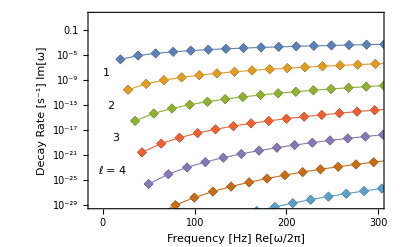

```mathematica
Show[ListLogPlot[LvGtab,(*Joined->True,*)PlotStyle->Directive[Black,Thickness[.002]],PlotMarkers->Style["◆",10],PlotRange->{{-10,300},{1*^-29,10^1.2}},Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω/2π]","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},
GridLines->{{},{300^-1}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{1,"1",{.03,0}},{10^-3,"",{.03,0}},{300^-1,"300^-1",0},{10^-6,"10^-6",{.03,0}},{10^-9,"",{.03,0}},{10^-12,"10^-12",{.03,0}},{10^-15,"",{.03,0}},{10^-18,"10^-18",{.03,0}},{10^-21,"",{.03,0}},{10^-24,"10^-24",{.03,0}},{10^-27,"",{.03,0}},{10^-1,""},{10^-2,""},{10^-4,""},{10^-5,""},{10^-7,""},{10^-8,""},{10^-10,""},{10^-11,""},{10^-13,""},{10^-14,""},{10^-16,""},{10^-17,""},{10^-19,""},{10^-20,""},{10^-22,""},{10^-23,""},{10^-25,""},{10^-26,""},{10^-28,""}},(*Right*)Automatic},{(*Bottom*){{0,"0",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"50",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"100",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"150",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"200",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"250",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"300",{.03,0}}},(*Top*){{0,"",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"",{.03,0}}}}}],
ListLogPlot[LvFtab,Joined->True,PlotMarkers->{"◆", 10},PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 4",{-5,-56},{-1,-1}],
Text["3",{10,-44},{-1,-1}],
Text["2",{5,-32},{-1,-1}],
Text["1",{0,-20},{-1,-1}]}]]
```

```mathematica
xmth[[1]]
```

{2.874020397753885207482197891569156883134408966502123835589744912×10^-64+581. ⅈ}

```mathematica
Table[{10 l,""},{l,0,30}]
```

```mathematica
LvHtab=Table[{(zshift/(2π τ))ReIm[xmth][[l,n,1]],(zshift/τ)ReIm[xmth][[l,n,2]]},{l,20},{n,Length[xmrtot[[l]]]}];
```

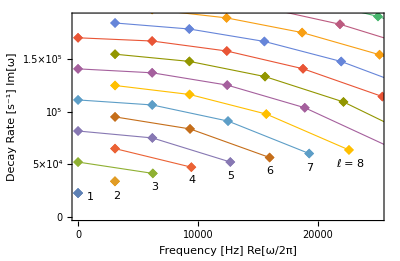

```mathematica
Show[ListPlot[LvHtab,Joined->False,PlotStyle->Thickness[.002],(*PlotStyle->Black,*)PlotMarkers->Style["◆",10],PlotRange->{{-4,25000},{0,190000}},AspectRatio->1/(.945GoldenRatio),Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω/2π]","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},GridLines->{{},{}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{0,"0"},{5 10^4,"5×10^4",{.03,0}},{10^5,"10^5",{.03,0}},{1.5 10^5,"1.5×10^5",{.03,0}},{2 10^5,"2×10^5",{.03,0}},
{10000,""},{20000,""},{30000,""},{40000,""},{60000,""},{70000,""},{80000,""},{90000,""},
{110000,""},{120000,""},{130000,""},{140000,""},{160000,""},{170000,""},{180000,""},{190000,""}},
(*Right*){{10000,""},{20000,""},{30000,""},{40000,""},{50000,"",{.03,0}},{60000,""},{70000,""},{80000,""},{90000,""},{100000,"",{.03,0}},{110000,""},{120000,""},{130000,""},{140000,""},{150000,"",{.03,0}},{160000,""},{170000,""},{1800000,""},{190000,""},{200000,"",{.03,0}}}},{(*Bottom*){{0,"0",{0,0}},{1000,""},{2000,""},{3000,""},{4000,""},{5000,"5000",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"10000",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"15000",{.03,0}},{16000,""},{17000,""},{18000,""},{19000,""},{20000,"20000",{.03,0}},{21000,""},{22000,""},{23000,""},{24000,""},{25000,"25000",{.03,0}},{26000,""},{27000,""},{28000,""},{29000,""},{30000,"30000"}},
(*Top*){{0,"",{0,0}},{1000,""},{2000,""},{3000,""},{4000,""},{5000,"",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"",{.03,0}},{16000,""},{17000,""},{18000,""},{19000,""},{20000,"",{.03,0}},{21000,""},{22000,""},{23000,""},{24000,""},{25000,"",{.03,0}},{26000,""},{270000,""},{28000,""},{29000,""},{30000,""}}}}],
ListPlot[LvHtab,PlotMarkers->{"◆", 10},Joined->True,PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 8",{21500,45000},{-1,-1}],
Text["7",{19000,41500},{-1,-1}],
Text["6",{15700,39000},{-1,-1}],
Text["5",{12400,34000},{-1,-1}],
Text["4",{9200,30000},{-1,-1}],
Text["3",{6100,23000},{-1,-1}],
Text["2",{2900,15000},{-1,-1}],
Text["1",{700,14000},{-1,-1}]}]]
```

### c370

```mathematica
zshft
```

0.765868

```mathematica
LvFtab=Table[{ zshift(2π τ)^-1 Re[ww[n,l]],(zshft/τ)Im[ww[n,l]]},{l,10},{n,50}];
LvGtab=Table[{zshift(2π τ)^-1 Chop[zf[[l,n]]],(zshft/τ)(1/11 γt^(2l+1)Chop[zf[[l,n]]]^(2l)/((2l-1)!!)^2(1-((l+2)(l-1))/(zf[[l,n]])^2)^-1)},{l,10},{n,23}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

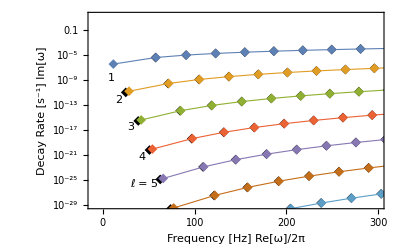

```mathematica
Show[ListLogPlot[LvGtab(*G*),(*Joined->True,*)PlotStyle->Directive[Black,Thickness[.002]],PlotMarkers->Style["◆",10],PlotRange->{{-10,300},{1*^-29,10^1.2}},Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω]/2π","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},
GridLines->{{},{300^-1}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{1,"1",{.03,0}},{10^-3,"",{.03,0}},{300^-1,"300^-1",0},{10^-6,"10^-6",{.03,0}},{10^-9,"",{.03,0}},{10^-12,"10^-12",{.03,0}},{10^-15,"",{.03,0}},{10^-18,"10^-18",{.03,0}},{10^-21,"",{.03,0}},{10^-24,"10^-24",{.03,0}},{10^-27,"",{.03,0}},{10^-1,""},{10^-2,""},{10^-4,""},{10^-5,""},{10^-7,""},{10^-8,""},{10^-10,""},{10^-11,""},{10^-13,""},{10^-14,""},{10^-16,""},{10^-17,""},{10^-19,""},{10^-20,""},{10^-22,""},{10^-23,""},{10^-25,""},{10^-26,""},{10^-28,""}},(*Right*)Automatic},{(*Bottom*){{0,"0",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"50",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"100",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"150",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"200",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"250",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"300",{.03,0}}},(*Top*){{0,"",{.03,0}},{10,""},{20,""},{30,""},{40,""},{50,"",{.03,0}},{60,""},{70,""},{80,""},{90,""},{100,"",{.03,0}},{110,""},{120,""},{130,""},{140,""},{150,"",{.03,0}},{160,""},{170,""},{180,""},{190,""},{200,"",{.03,0}},{210,""},{220,""},{230,""},{240,""},{250,"",{.03,0}},{260,""},{270,""},{280,""},{290,""},{300,"",{.03,0}}}}}],
ListLogPlot[LvFtab,Joined->True,PlotMarkers->{"◆", 10},PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["ℓ = 5",{30,-61},{-1,-1}],
Text["4",{39,-51},{-1,-1}],
Text["3",{27,-40},{-1,-1}],
Text["2",{13,-30},{-1,-1}],
Text["1",{5,-22},{-1,-1}]}]]
```

```mathematica
zf[[2]]^2
```

{6.2556643848759751890183159333,50.92262148221472152001028469,110.55683535477113200714264972,189.65911458111610522426503111,288.42416534009599630576643545,406.89782534735608057858761559,545.09592848976367207243276304,703.02520865121879548150745555,880.68894384147007388011485973,1078.0888908711063161731439197,1295.2260620802183921848683146,1532.1010749424500930302217341,1788.7143237735562216864581143,2065.0660701085332963513761196,2361.1564930301958310860991914,2676.9857185428221816121694802,3012.5538374109005969443763009,3367.8609163688324795634849619,3742.9070053770019275080927053,4137.6921424424451868321725232,4552.2163568961158597060123084,4986.4796716670900573969854154,5440.4821048900513495041146394,5914.2236710605636055986756979,6407.7043818779661850844976312,6920.9242468688716118940986177,7453.8832738542157777018922124,8006.5814693031876217029864669,8579.018838604313505670704801,9171.1953862751481638399049146}

```mathematica
xmth[[1]]
```

{2.874020397753885207482197891569156883134408966502123835589744912×10^-64+581. ⅈ}

```mathematica
Table[{10 l,""},{l,0,30}]
```

```mathematica
LvHtab=Table[{(zshift/(2π τ))ReIm[xmth][[l,n,1]],(zshift/τ)ReIm[xmth][[l,n,2]]},{l,20},{n,Length[xmth[[l]]]}];
```

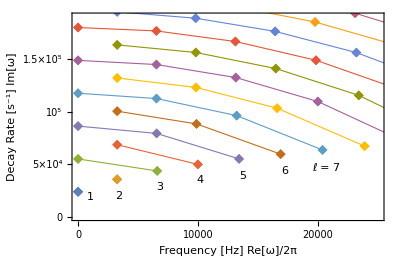

```mathematica
Show[ListPlot[LvHtab,Joined->False,PlotStyle->Thickness[.002],(*PlotStyle->Black,*)PlotMarkers->Style["◆",10],PlotRange->{{-4,25000},{0,190000}},AspectRatio->1/(.945GoldenRatio),Frame->True,FrameLabel->{"Frequency [Hz]   Re[ω]/2π","Decay Rate [s^-1]   Im[ω]"},LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},GridLines->{{},{}},FrameStyle->Directive[Black,Thickness[.002]],FrameTicks->{{(*Left*){{0,"0"},{5 10^4,"5×10^4",{.03,0}},{10^5,"10^5",{.03,0}},{1.5 10^5,"1.5×10^5",{.03,0}},{2 10^5,"2×10^5",{.03,0}},
{10000,""},{20000,""},{30000,""},{40000,""},{60000,""},{70000,""},{80000,""},{90000,""},
{110000,""},{120000,""},{130000,""},{140000,""},{160000,""},{170000,""},{180000,""},{190000,""}},
(*Right*){{10000,""},{20000,""},{30000,""},{40000,""},{50000,"",{.03,0}},{60000,""},{70000,""},{80000,""},{90000,""},{100000,"",{.03,0}},{110000,""},{120000,""},{130000,""},{140000,""},{150000,"",{.03,0}},{160000,""},{170000,""},{1800000,""},{190000,""},{200000,"",{.03,0}}}},{(*Bottom*){{0,"0",{0,0}},{1000,""},{2000,""},{3000,""},{4000,""},{5000,"5000",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"10000",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"15000",{.03,0}},{16000,""},{17000,""},{18000,""},{19000,""},{20000,"20000",{.03,0}},{21000,""},{22000,""},{23000,""},{24000,""},{25000,"25000",{.03,0}},{26000,""},{27000,""},{28000,""},{29000,""},{30000,"30000"}},
(*Top*){{0,"",{0,0}},{1000,""},{2000,""},{3000,""},{4000,""},{5000,"",{.03,0}},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"",{.03,0}},{11000,""},{12000,""},{13000,""},{14000,""},{15000,"",{.03,0}},{16000,""},{17000,""},{18000,""},{19000,""},{20000,"",{.03,0}},{21000,""},{22000,""},{23000,""},{24000,""},{25000,"",{.03,0}},{26000,""},{270000,""},{28000,""},{29000,""},{30000,""}}}}],
ListPlot[LvHtab,PlotMarkers->{"◆", 10},Joined->True,PlotStyle->Thickness[.002]],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
(*Text["ℓ = 8",{21500,45000},{-1,-1}],*)
Text["ℓ = 7",{19500,41500},{-1,-1}],
Text["6",{16900,39000},{-1,-1}],
Text["5",{13400,34000},{-1,-1}],
Text["4",{9900,30000},{-1,-1}],
Text["3",{6500,23000},{-1,-1}],
Text["2",{3100,15000},{-1,-1}],
Text["1",{700,14000},{-1,-1}]}]]
```

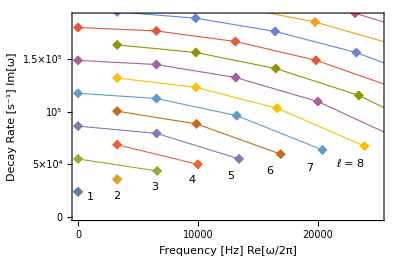

```mathematica
xmth[[1]]
```

{1.72237566411171005052525627650185057843777209567974045305394021×10^-67+370.0891383374513850067009170113985971509109660506272171767052768 ⅈ}

### Dunno

```mathematica
Abs[ω]Sin[ω t]Cos[ω t]/.ω->a+ⅈ b
```

```mathematica
(*Abs[a+ⅈ b]*)Cos[(a+ⅈ b) t] Sin[(a+ⅈ b) t]//ComplexExpand
CoefficientList[Cos[a t]^2 Cosh[b t]^2-2 i Cos[a t] Cosh[b t] Sin[a t] Sinh[b t]-Sin[a t]^2 Sinh[b t]^2,i]
```

Cos[a t] Cosh[b t]^2 Sin[a t]+Cos[a t] Sin[a t] Sinh[b t]^2+ⅈ (Cos[a t]^2 Cosh[b t] Sinh[b t]-Cosh[b t] Sin[a t]^2 Sinh[b t])

{Cos[a t]^2 Cosh[b t]^2-Sin[a t]^2 Sinh[b t]^2,-2 Cos[a t] Cosh[b t] Sin[a t] Sinh[b t]}

```mathematica
%647
```

```mathematica
Cosh[b t]^2-2 ⅈ  Cosh[b t]  Sinh[b t]- Sinh[b t]^2//Simplify
```

1-ⅈ Sinh[2 b t]

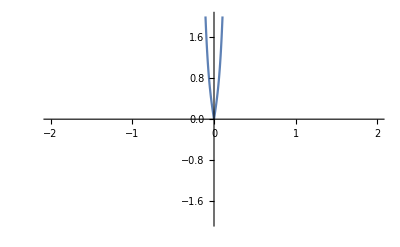

```mathematica
Plot[Abs[(*Abs[a+ⅈ b] *)Cos[(a-ⅈ b) t] Sin[(a+ⅈ b) t]]/.{a->3,b->10.0}//Evaluate,{t,-2,2},PlotRange->{-2,2}]
```

```mathematica
Series[Evaluate[D[Log[SphericalHankelH1[l,a z]],z]],{a,0,3}]
```

(ⅇ^(-2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]-2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) (a^(2 l) ⅇ^(2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+4 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) ((ⅈ 2^(-5/2-l) z^(1+l) Cos[(3/2+l) π] Gamma[-3/2-l] a^2)/π+O[a]^4)+a^(2 l) ⅇ^(2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+4 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) (-(2^(-5/2-l) z^(1+l) a^2)/Gamma[5/2+l]+O[a]^4)+a^(2 l) ⅇ^(2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+4 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) ((ⅈ 2^(-3/2-l) z^(-1+l) Cos[(1/2+l) π] Gamma[-1/2-l])/π-(ⅈ 2^(-7/2-l) z^(1+l) Cos[(1/2+l) π] Gamma[-1/2-l] a^2)/((3/2+l) π)+O[a]^3)+a^(2 l) ⅇ^(4 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) (-(ⅈ 2^(-1/2-l) z^(-1+l) Cos[(-1/2+l) π] Gamma[1/2-l])/π+(ⅈ 2^(-5/2-l) z^(1+l) Cos[(-1/2+l) π] Gamma[1/2-l] a^2)/((1/2+l) π)+O[a]^3)+ⅇ^(2 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) (-(ⅈ 2^(-3/2+l) z^-l Gamma[-1/2+l] a)/π-(ⅈ 2^(-5/2+l) z^(2-l) Gamma[-1/2+l] a^3)/((-3+2 l) π)+O[a]^4)+a^(2 l) ⅇ^(4 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) ((2^(-1/2-l) z^(-1+l))/Gamma[1/2+l]-(2^(-5/2-l) z^(1+l) a^2)/((1/2+l) Gamma[1/2+l])+O[a]^3)+ⅇ^(2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) ((ⅈ 2^(-1/2+l) z^(-2-l) Gamma[1/2+l])/(π a)+(ⅈ 2^(-3/2+l) z^-l Gamma[1/2+l] a)/((-1+2 l) π)+O[a]^2)+a^(2 l) ⅇ^(2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+4 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (3/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) (-(2^(-3/2-l) z^(-1+l))/Gamma[3/2+l]+(2^(-7/2-l) z^(1+l) a^2)/((3/2+l) Gamma[3/2+l])+O[a]^3)+ⅇ^(2 ⅈ (-1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]+2 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) ((ⅈ 2^(1/2+l) z^(-2-l) Gamma[3/2+l])/(π a)+(ⅈ 2^(-1/2+l) z^-l Gamma[3/2+l] a)/((1+2 l) π)+O[a]^2)))/(a^(2 l) ⅇ^(4 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) (-(ⅈ 2^(-1/2-l) z^l Cos[(1/2+l) π] Gamma[-1/2-l])/π+(ⅈ 2^(-5/2-l) z^(2+l) Cos[(1/2+l) π] Gamma[-1/2-l] a^2)/((3/2+l) π)+O[a]^3)+(-(ⅈ 2^(1/2+l) z^(-1-l) Gamma[1/2+l])/(π a)-(ⅈ 2^(-1/2+l) z^(1-l) Gamma[1/2+l] a)/((-1+2 l) π)+O[a]^3)+a^(2 l) ⅇ^(4 ⅈ (1/2+l) π Floor[(π-Arg[a]-Arg[z])/(2 π)]) ((2^(-1/2-l) z^l)/Gamma[3/2+l]-(2^(-5/2-l) z^(2+l) a^2)/((3/2+l) Gamma[3/2+l])+O[a]^3))

```mathematica
αl=Table[
Series[Evaluate[D[Log[SphericalHankelH1[l,a z]],z]],{a,0,2l+1}],{l,10}]
```

{-2/z+z a^2+ⅈ z^2 a^3+O[a]^(7/2),-3/z+(z a^2)/3+(z^3 a^4)/9+1/9 ⅈ z^4 a^5+O[a]^(11/2),-4/z+(z a^2)/5+(z^3 a^4)/75+(2 z^5 a^6)/375+1/225 ⅈ z^6 a^7+O[a]^(15/2),-5/z+(z a^2)/7+(z^3 a^4)/245+(2 z^5 a^6)/5145+(23 z^7 a^8)/180075+(ⅈ z^8 a^9)/11025+O[a]^(19/2),-6/z+(z a^2)/9+(z^3 a^4)/567+(2 z^5 a^6)/25515+(11 z^7 a^8)/1607445+(26 z^9 a^10)/14467005+(ⅈ z^10 a^11)/893025+O[a]^(23/2),-7/z+(z a^2)/11+(z^3 a^4)/1089+(2 z^5 a^6)/83853+(43 z^7 a^8)/41507235+(106 z^9 a^10)/1369738755+(5234 z^11 a^12)/316409652405+(ⅈ z^12 a^13)/108056025+O[a]^(27/2),-8/z+(z a^2)/13+(z^3 a^4)/1859+(2 z^5 a^6)/217503+(53 z^7 a^8)/217720503+(134 z^9 a^10)/14151832695+(32842 z^11 a^12)/54640226035395+(15220 z^13 a^14)/142064587692027+(ⅈ z^14 a^15)/18261468225+O[a]^(31/2),-9/z+(z a^2)/15+(z^3 a^4)/2925+(2 z^5 a^6)/482625+(7 z^7 a^8)/94111875+(2 z^9 a^10)/1097971875+(1318 z^11 a^12)/21196347046875+(1076 z^13 a^14)/317945205703125+(31891 z^15 a^16)/61999315112109375+(ⅈ z^16 a^17)/4108830350625+O[a]^(35/2),-10/z+(z a^2)/17+(z^3 a^4)/4335+(2 z^5 a^6)/958035+(73 z^7 a^8)/2687288175+(38 z^9 a^10)/82231018155+(32374 z^11 a^12)/3180284627144625+(49444 z^13 a^14)/162194515984375875+(936511 z^15 a^16)/64993659619453475625+(191383694 z^17 a^18)/100545191431294526791875+(ⅈ z^18 a^19)/1187451971330625+O[a]^(39/2),-11/z+(z a^2)/19+(z^3 a^4)/6137+(2 z^5 a^6)/1749045+(83 z^7 a^8)/7344239955+(218 z^9 a^10)/1534946150595+(148294 z^11 a^12)/66931326896694975+(388316 z^13 a^14)/8901866477260431675+(215540113 z^15 a^16)/186894686690082763016625+(1532860594 z^17 a^18)/31958991424004152475842875+(635271659786 z^19 a^20)/113550296529486753746669734875+(ⅈ z^20 a^21)/428670161650355625+O[a]^(43/2)}

```mathematica
αl//TableForm
```

-2/z+z a^2+ⅈ z^2 a^3+O[a]^(7/2)
-3/z+(z a^2)/3+(z^3 a^4)/9+1/9 ⅈ z^4 a^5+O[a]^(11/2)
-4/z+(z a^2)/5+(z^3 a^4)/75+(2 z^5 a^6)/375+1/225 ⅈ z^6 a^7+O[a]^(15/2)
-5/z+(z a^2)/7+(z^3 a^4)/245+(2 z^5 a^6)/5145+(23 z^7 a^8)/180075+(ⅈ z^8 a^9)/11025+O[a]^(19/2)
-6/z+(z a^2)/9+(z^3 a^4)/567+(2 z^5 a^6)/25515+(11 z^7 a^8)/1607445+(26 z^9 a^10)/14467005+(ⅈ z^10 a^11)/893025+O[a]^(23/2)
-7/z+(z a^2)/11+(z^3 a^4)/1089+(2 z^5 a^6)/83853+(43 z^7 a^8)/41507235+(106 z^9 a^10)/1369738755+(5234 z^11 a^12)/316409652405+(ⅈ z^12 a^13)/108056025+O[a]^(27/2)
-8/z+(z a^2)/13+(z^3 a^4)/1859+(2 z^5 a^6)/217503+(53 z^7 a^8)/217720503+(134 z^9 a^10)/14151832695+(32842 z^11 a^12)/54640226035395+(15220 z^13 a^14)/142064587692027+(ⅈ z^14 a^15)/18261468225+O[a]^(31/2)
-9/z+(z a^2)/15+(z^3 a^4)/2925+(2 z^5 a^6)/482625+(7 z^7 a^8)/94111875+(2 z^9 a^10)/1097971875+(1318 z^11 a^12)/21196347046875+(1076 z^13 a^14)/317945205703125+(31891 z^15 a^16)/61999315112109375+(ⅈ z^16 a^17)/4108830350625+O[a]^(35/2)
-10/z+(z a^2)/17+(z^3 a^4)/4335+(2 z^5 a^6)/958035+(73 z^7 a^8)/2687288175+(38 z^9 a^10)/82231018155+(32374 z^11 a^12)/3180284627144625+(49444 z^13 a^14)/162194515984375875+(936511 z^15 a^16)/64993659619453475625+(191383694 z^17 a^18)/100545191431294526791875+(ⅈ z^18 a^19)/1187451971330625+O[a]^(39/2)
-11/z+(z a^2)/19+(z^3 a^4)/6137+(2 z^5 a^6)/1749045+(83 z^7 a^8)/7344239955+(218 z^9 a^10)/1534946150595+(148294 z^11 a^12)/66931326896694975+(388316 z^13 a^14)/8901866477260431675+(215540113 z^15 a^16)/186894686690082763016625+(1532860594 z^17 a^18)/31958991424004152475842875+(635271659786 z^19 a^20)/113550296529486753746669734875+(ⅈ z^20 a^21)/428670161650355625+O[a]^(43/2)

```mathematica
αlⅈ=Table[(-ⅈ z^(-2l) CoefficientList[Normal[αl],a][[l,-1]])^-1,{l,10}]
```

{1,9,225,11025,893025,108056025,18261468225,4108830350625,1187451971330625,428670161650355625}

```mathematica
Gamma[5/2]
```

(3 √π)/4

```mathematica
Table[((2l-1)!!)^2,{l,10}]
```

{1,9,225,11025,893025,108056025,18261468225,4108830350625,1187451971330625,428670161650355625}

```mathematica
Table[1/1.26(2l-1/2)!//N,{l,10}]
```

{1.05503,9.23153,228.48,11138.4,899427.,1.08606×10^8,1.83272×10^10,4.11905×10^12,1.18937×10^15,4.29067×10^17}

```mathematica
Log10[αlⅈ]//N
```

{0.,0.954243,2.35218,4.04238,5.95086,8.03365,10.2615,12.6137,15.0746,17.6321}

```mathematica
%824-%826
```

{0.123636,0.111402,0.107037,0.104815,0.103473,0.102575,0.101932,0.101449,0.101073,0.100772}

```mathematica
10^(.1)
```

1.25893

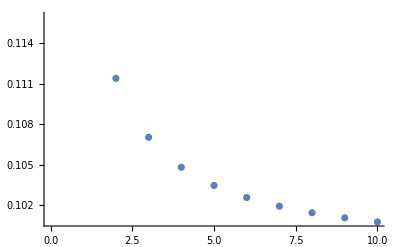

```mathematica
ListPlot[%827]
```

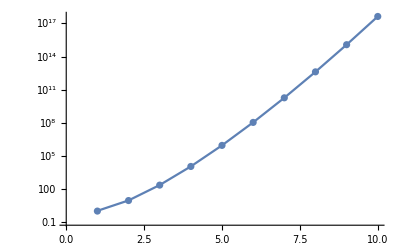

```mathematica
Show[ListLogPlot[αlⅈ],
ListLogPlot[Transpose[Table[{(*{l,ⅇ^(l^1.66-1)},*){l,1/1.26 Gamma[2l+1/2]}},{l,10}]],Joined->True]]
```